```mathematica
SetDirectory[NotebookDirectory[]];
(* Download the l1PackV2 Mathematica package *)
ExtractArchive[ExtractArchive[URLDownload["https://prod-dcd-datasets-cache-zipfiles.s3.eu-west-1.amazonaws.com/sz2z8gw8sz-1.zip"],OverwriteTarget -> True][[1]],"l1packV2",OverwriteTarget -> True];
SetDirectory["l1packV2"];
<<L1Packv2`
SetDirectory[NotebookDirectory[]];
```

# Create a library of gates from Clifford+T sequences

```mathematica
(* function that converts a Clifford+T sequence into a unitary operator *)
unitaryFromGateSequence[sequence_]:=Module[{Hgate,Sgate,Tgate,Xgate,Wgate,chars,mats,gate},
Hgate={{1/(√2),1/(√2)},{1/(√2),-1/(√2)}};
Sgate={{1,0},{0,ⅈ}};
Tgate={{1,0},{0,ⅇ^((ⅈ π)/4)}};
Xgate={{0,1},{1,0}};
Wgate=IdentityMatrix[2]*Exp[ⅈ*π/4];
chars=Characters[sequence];
mats=N[chars/.{"X"->Xgate,"H"->Hgate, "T"->Tgate,"S"->Sgate,"W"->Wgate},150];
gate=mats[[1]];
Do[
gate=gate.mats[[k]];
,{k,2,Length@mats}
];
Return@gate;
]
```

```mathematica
(* open library of Clifford+T sequences that were generate using the code provided in [arXiv:1403.2975] *)
sequences=Import["clifford_T.m"];
(* Append Clifford operations to the sequence to increase the size of the library *)
sequences=Join[sequences,({#<>"H",#<>"S",#<>"SH",#<>"HS"
,#<>"HSS",#<>"SSH",#<>"HSH",#<>"HSSH"
,#<>"SSHSS",#<>"HSHSH",#<>"HSSSHS"}&)@sequences[[1]]];
listOfUnitaries=(unitaryFromGateSequence/@sequences);
```

# Generate the design matrix and the target vector

```mathematica
transferMat[mat_]:=Re@Table[
Tr[PauliMatrix[k].ConjugateTranspose[mat.PauliMatrix[l].ConjugateTranspose[mat]]]/2,{k,0,3},{l,0,3}]

checkSol[sol_,designMatrix_,Udesired_]:={N@Log10[Norm[designMatrix.sol-Udesired]/4],N@Log10@Abs[Norm[sol,1]-1]};
```

```mathematica
(* Target vector as the vectorised process matrix of the target rotation *)
Udesired=Flatten@Import["target.m"];

(* The design matrix is obtained as a list of vectorised process matrices of the individual Clifford+T sequences *)
listOfTransferMats=transferMat/@listOfUnitaries;
designMatrix=Transpose@Join[
Table[Flatten[listOfTransferMats[[k]]],{k,1,Length@listOfTransferMats}]
];

(* Demonstrate solution using a least squares fit *)
solvec=Chop[PseudoInverse[designMatrix].Udesired];
Print["Measurement overhead using a least-squares solution:  ",StringForm["1+10^(``)",checkSol[solvec,designMatrix,Udesired][[2]]]]
```

Measurement overhead using a least-squares solution:  1+10^(RowBox[{)

# LARS l1 regularised solution

```mathematica
(* simple linear interpolation of the solution vector entries *)
interpolateVec[minimizers_,x_]:=Module[{vec,ind,remainder},
ind=Floor[x];
remainder=x-ind;
vec=(1-remainder)*minimizers[[ind]]+remainder*minimizers[[ind+1]];
Return@vec;
];
```

```mathematica
(* Run the LARS solver "FindMinimizer[...]" of the L1Packv2 until an exact solution is found using the option MinimumDiscrepancy->0 *)
solutionVectors=FindMinimizer[designMatrix,Udesired,Verbose->0,Exact->False,MinimumDiscrepancy->0,ListFunction:>Minimizer][[1]];
(* discard all solutions that are L1 overregularised, i.e., the norm of the solution vector is less than 1. *)
indexes=Flatten@Position[((Norm[#,1]>=1)&)/@solutionVectors,True];
solutionVectors=solutionVectors[[indexes]];


(* find solution with L1 norm = 1, i.e., no measurement overhead, using the option MaximumL1Norm->1*)
solL1norm=FindMinimizer[designMatrix,Udesired,Verbose->0,Exact->False,MaximumL1Norm->1];
solutionVectors=Prepend[solutionVectors,solL1norm];

Print["Exact solution:  ",MatrixForm@N@solutionVectors[[-1]] ,"       best approximate solution with no measurement overhead:   ",MatrixForm@N@solutionVectors[[1]] ]
```

Exact solution:  (0.
0.283574
0.0677463
0.
0.
0.
0.
0.
0.
0.288153
0.110988
0.
0.
0.
0.
0.248301
0.
0.
0.
0.0012387
0.
0.
-3.34481×10^-8
0.
0.
-3.69909×10^-8
0.
0.
-2.08993×10^-8
0.
-1.06346×10^-8)       best approximate solution with no measurement overhead:   (0.
0.354911
0.00767578
0.
0.
0.
0.
0.
0.
0.398772
0.135098
0.
0.
0.
0.
0.103542
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

# Plot tradeoff curve

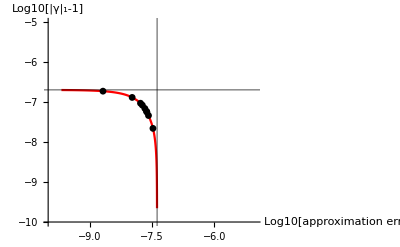

```mathematica
discreteSolutions=((checkSol[#,designMatrix,Udesired])&)/@(solutionVectors);
interpolatedSolutions=Table[
checkSol[interpolateVec[solutionVectors,k],designMatrix,Udesired]
,{k,1,Length@solutionVectors-0.1,0.01}];

(* calculate asymptotic gridlines *)
errorAtNoOveread=checkSol[solutionVectors[[1]],designMatrix,Udesired][[1]];
overheadAtNoError=checkSol[solutionVectors[[-1]],designMatrix,Udesired][[2]];


Show[
ListLinePlot[interpolatedSolutions
,PlotRange->{{-10,-5},{-10,-5}}
,GridLines->{{errorAtNoOveread},{overheadAtNoError}}
,GridLinesStyle->Black
,PlotStyle->Red
,AxesLabel->{"Log10[approximation error]","Log10[|γ|_1-1]"}
,AxesOrigin->{-10,-10}
,ImageSize->400
]
,
ListPlot[discreteSolutions,PlotMarkers->{Automatic, Small},PlotStyle->Black
]
]
```